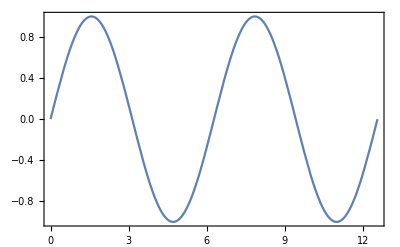

```mathematica
Plot[Sin[ x],{x,0,4Pi}, Frame->True, Axes->False, LabelStyle->Opacity[0]]
```

```mathematica
Plot[Sin[ x],{x,0,4Pi}, LabelStyle->Opacity[0], ImagePadding->{{1,1},{40,1}}]
```

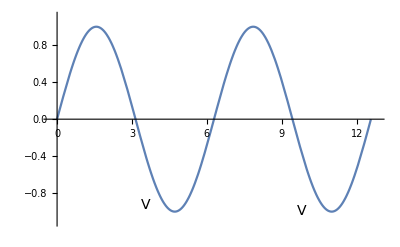

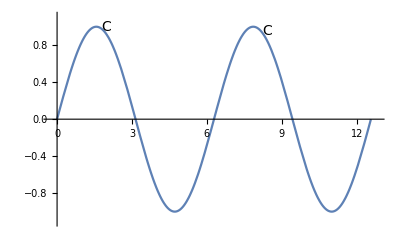

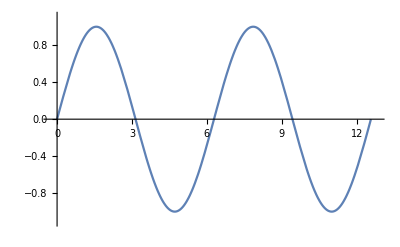

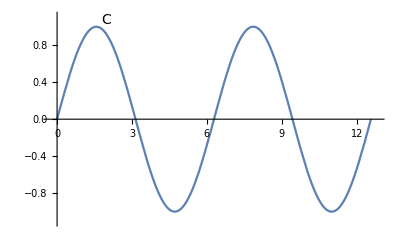

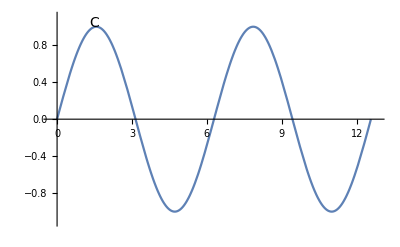

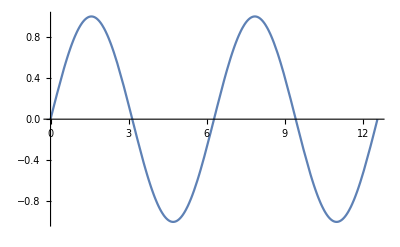

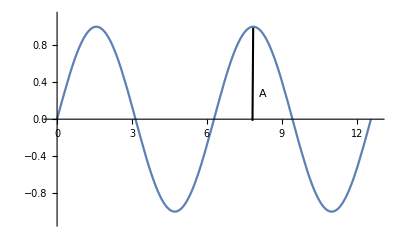

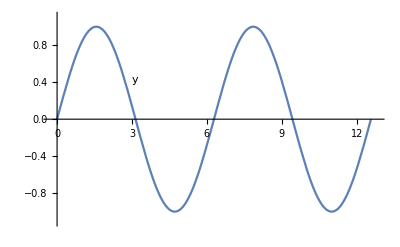

```mathematica
Plot[Sin[ x],{x,0,6Pi}, LabelStyle->Opacity[0], ImagePadding->{{1,1},{1, 40}}]
```

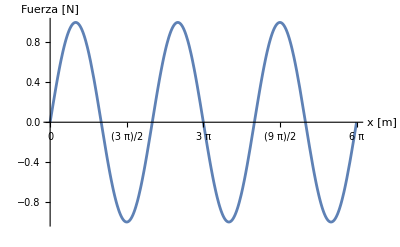

plot.eps

```mathematica
Plot[Sin[ x],{x,0,6Pi}, Ticks->{Range[0,6Pi,Pi/2],Automatic}, AxesLabel->{"x [m]","Fuerza [N]" }, LabelStyle->Directive[Black]]
Export["plot.eps",First@ImportString[ExportString[plot,"PDF"]]]
```